## Integration Test

Define a set of functions to be integrated

Define a set of intervals on which `NIntegrate` should be performed

Measure the timing performance of both version of Mathematica

```mathematica
myFunction[k_,a_]:=Sum[i*a*Sin[#]^i,{i,k,0,-1}]&[x];
functionGrupx[n_,a_]:=Table[myFunction[k,a][x],{k,1,n}];
t25=Table[i,{i,1,25,1}];
t55=Table[i,{i,1,50,1}];
t75=Table[i,{i,1,75,1}];
t[ops_]:=Table[i,{i,1,ops,1}];
```

### Example with t

```mathematica
t[5]
t[12]
```

{1,2,3,4,5}

{1,2,3,4,5,6,7,8,9,10,11,12}

### Create threaded operation

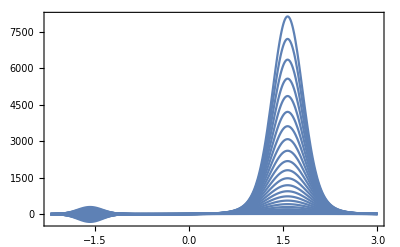

```mathematica
(*(list of functions)*)
thop[lister_]:=MapThread[myFunction,{lister,lister}];
Plot[thop[t25],{x,-2.2,3},PlotRange->Full,Frame->True,Axes->False]
```

### Example with thop (list of functions)

```mathematica
thop[t[0]]
thop[t[1]]
thop[t[3]]
```

{}

{Sin[x]}

{Sin[x],2 Sin[x]+4 Sin[x]^2,3 Sin[x]+6 Sin[x]^2+9 Sin[x]^3}

```mathematica
Do[Print[AbsoluteTiming[functionGrupx[100,1]][[1]]],{i,1,10,1}]
```

0.005877

0.005901

0.005796

0.005909

0.006102

0.005801

0.005976

0.005

0.005247

0.005036

```mathematica
Do[Print[AbsoluteTiming[thop[t[125]]][[1]]],{i,1,10,1}]
```

0.008898

0.00818

0.009575

0.008767

0.009418

0.009323

0.00896

0.008981

0.008538

0.00799

```mathematica
thop[t[2]]
```

{Sin[x],2 Sin[x]+4 Sin[x]^2}

```mathematica
numint[function_,interval_]:=NIntegrate[function,{x,interval[[1]],interval[[2]]}];
```

```mathematica
batchintegrater[functions_,intervals_]:=Table[numint[functions[[i]],intervals[[i]]],{i,1,Length[functions]}];
```

```mathematica
intervalmaker[n_]:=Table[{-π,π/6},{i,1,n}];
```

```mathematica
intervalmaker[7]
```

{{-π,π/6},{-π,π/6},{-π,π/6},{-π,π/6},{-π,π/6},{-π,π/6},{-π,π/6}}

```mathematica
AbsoluteTiming[pp=batchintegrater[thop[t[120]],intervalmaker[120]];Print[pp]]
```

{-1.86603,2.73231,-7.74721,8.63044,-15.8063,16.4202,-25.6163,25.7176,-36.8873,36.3317,-49.4292,48.1315,-63.1122,61.0168,-77.8414,74.9079,-93.5434,89.7401,-110.159,105.459,-127.637,122.02,-145.937,139.383,-165.021,157.514,-184.858,176.382,-205.418,195.962,-226.677,216.228,-248.612,237.159,-271.201,258.735,-294.426,280.938,-318.27,303.751,-342.715,327.159,-367.748,351.147,-393.354,375.702,-419.521,400.811,-446.237,426.463,-473.49,452.647,-501.269,479.353,-529.565,506.57,-558.367,534.29,-587.668,562.503,-617.459,591.202,-647.731,620.378,-678.476,650.025,-709.689,680.134,-741.36,710.699,-773.484,741.714,-806.054,773.172,-839.065,805.067,-872.51,837.393,-906.383,870.145,-940.679,903.318,-975.393,936.905,-1010.52,970.903,-1046.05,1005.31,-1081.99,1040.11,-1118.33,1075.31,-1155.06,1110.9,-1192.18,1146.88,-1229.69,1183.25,-1267.57,1219.99,-1305.84,1257.11,-1344.48,1294.6,-1383.49,1332.47,-1422.87,1370.69,-1462.61,1409.28,-1502.71,1448.23,-1543.17,1487.53,-1583.98,1527.18,-1625.14,1567.19,-1666.65,1607.53}

{44.224,Null}